```mathematica
(* ===ПАРАМЕТРЫ ДЛЯ МОДЫ n===*)n=6;(*выбери нужную моду*)α=(π n)/w;

(*Неизвестные для данной моды*)
varsN={An[1],Bn[1],An[2],Bn[2],An[3],Bn[3],An[4],Bn[4],An[5],Bn[5],An[6],Bn[6],An[7],Bn[7],An[8],Bn[8],An[9],Bn[9]};

(*Уравнения непрерывности на стыках*)

(*Стык 1-2*)
eqN2=An[1] Sinh[α y1]+Bn[1] Cosh[α y1]==An[2] Sinh[α y1]+Bn[2] Cosh[α y1];
eqN3=k1 (An[1] Cosh[α y1]+Bn[1] Sinh[α y1])==k2 (An[2] Cosh[α y1]+Bn[2] Sinh[α y1]);

(*Стык 2-3*)
eqN4=An[2] Sinh[α y2]+Bn[2] Cosh[α y2]==An[3] Sinh[α y2]+Bn[3] Cosh[α y2];
eqN5=k2 (An[2] Cosh[α y2]+Bn[2] Sinh[α y2])==k3 (An[3] Cosh[α y2]+Bn[3] Sinh[α y2]);

(*Стык 3-4*)
eqN6=An[3] Sinh[α y3]+Bn[3] Cosh[α y3]==An[4] Sinh[α y3]+Bn[4] Cosh[α y3];
eqN7=k3 (An[3] Cosh[α y3]+Bn[3] Sinh[α y3])==k4 (An[4] Cosh[α y3]+Bn[4] Sinh[α y3]);

(*Стык 4-5*)
eqN8=An[4] Sinh[α y4]+Bn[4] Cosh[α y4]==An[5] Sinh[α y4]+Bn[5] Cosh[α y4];
eqN9=k4 (An[4] Cosh[α y4]+Bn[4] Sinh[α y4])==k5 (An[5] Cosh[α y4]+Bn[5] Sinh[α y4]);

(*Стык 5-6*)
eqN10=An[5] Sinh[α y5]+Bn[5] Cosh[α y5]==An[6] Sinh[α y5]+Bn[6] Cosh[α y5];
eqN11=k5 (An[5] Cosh[α y5]+Bn[5] Sinh[α y5])==k6 (An[6] Cosh[α y5]+Bn[6] Sinh[α y5]);

(*Стык 6-7*)
eqN12=An[6] Sinh[α y6]+Bn[6] Cosh[α y6]==An[7] Sinh[α y6]+Bn[7] Cosh[α y6];
eqN13=k6 (An[6] Cosh[α y6]+Bn[6] Sinh[α y6])==k7 (An[7] Cosh[α y6]+Bn[7] Sinh[α y6]);

(*Стык 7-8*)
eqN14=An[7] Sinh[α y7]+Bn[7] Cosh[α y7]==An[8] Sinh[α y7]+Bn[8] Cosh[α y7];
eqN15=k7 (An[7] Cosh[α y7]+Bn[7] Sinh[α y7])==k8 (An[8] Cosh[α y7]+Bn[8] Sinh[α y7]);

(*Стык 8-9*)
eqN16=An[8] Sinh[α y8]+Bn[8] Cosh[α y8]==An[9] Sinh[α y8]+Bn[9] Cosh[α y8];
eqN17=k8 (An[8] Cosh[α y8]+Bn[8] Sinh[α y8])==k9 (An[9] Cosh[α y8]+Bn[9] Sinh[α y8]);

(*Верхнее условие (провод)*)
fn=(2 qr/(π n)) (Sin[α b]-Sin[α a]);
eqN18=α (An[9] Cosh[α y9]+Bn[9] Sinh[α y9])==fn;
(*Нижнее условие:теплоизоляция для моды n*)eqN1=An[1]==0;

(*Полная система для моды n*)
systemNfull={eqN1,eqN2,eqN3,eqN4,eqN5,eqN6,eqN7,eqN8,eqN9,eqN10,eqN11,eqN12,eqN13,eqN14,eqN15,eqN16,eqN17,eqN18};

solutionN=NSolve[systemNfull,varsN]
```

```mathematica
{{An[1]->-3.714660555723216*^-14,Bn[1]->150.45045936093936,An[2]->-25.140109827437417,Bn[2]->156.04198034795846,An[3]->16.8423670556328,Bn[3]->145.06568013582924,An[4]->-31.22506894706495,Bn[4]->159.71597384997898,An[5]->245.5080263322119,Bn[5]->45.864664291486925,An[6]->-33.364886562939624,Bn[6]->162.42442357473672,An[7]->136.56630317491727,Bn[7]->75.13010203780854,An[8]->136.5663031749173,Bn[8]->75.13010203780853,An[9]->-32.789665711982366,Bn[9]->173.30414448715607}}
```

{{An[1]→-3.71466×10^-14,Bn[1]→150.45,An[2]→-25.1401,Bn[2]→156.042,An[3]→16.8424,Bn[3]→145.066,An[4]→-31.2251,Bn[4]→159.716,An[5]→245.508,Bn[5]→45.8647,An[6]→-33.3649,Bn[6]→162.424,An[7]→136.566,Bn[7]→75.1301,An[8]→136.566,Bn[8]→75.1301,An[9]→-32.7897,Bn[9]→173.304}}

```mathematica
(* ==========ФИЗИЧЕСКИЕ ПАРАМЕТРЫ==========*)w=400*10^-6;
L=4*10^-3;

y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

k1=10;k2=55;k3=10;k4=55;k5=10;
k6=55;k7=10;k8=10;k9=55;

h=25; Tamb=293;

q1=-2.44141*10^10;
q2=-5.07813*10^9;
q3=-9.76563*10^10;
q4=-3.04688*10^11;
q5=-2.48*10^15;
q6=-1.62891*10^11;
q7=-5.42969*10^10;
q8=-1.52344*10^10;
q9=-8.71094*10^8;

a=150*10^-6;b=250*10^-6;qr=-2*10^5;(*поток от провода*)f0=qr (b-a)/w;

(* ==========СИСТЕМА ДЛЯ ЧАСТНОГО РЕШЕНИЯ (n=0)==========*)

vars0={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(* Нижнее условие: конвекция на дне *)
eqBottom=B0[1]==293;

(*Стык 1-2*)
eq2=q1/(2 k1) y1^2+A0[1] y1+B0[1]==q2/(2 k2) y1^2+A0[2] y1+B0[2];
eq3=q1 y1+k1 A0[1]==q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=q2/(2 k2) y2^2+A0[2] y2+B0[2]==q3/(2 k3) y2^2+A0[3] y2+B0[3];
eq5=q2 y2+k2 A0[2]==q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=q3/(2 k3) y3^2+A0[3] y3+B0[3]==q4/(2 k4) y3^2+A0[4] y3+B0[4];
eq7=q3 y3+k3 A0[3]==q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=q4/(2 k4) y4^2+A0[4] y4+B0[4]==q5/(2 k5) y4^2+A0[5] y4+B0[5];
eq9=q4 y4+k4 A0[4]==q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=q5/(2 k5) y5^2+A0[5] y5+B0[5]==q6/(2 k6) y5^2+A0[6] y5+B0[6];
eq11=q5 y5+k5 A0[5]==q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=q6/(2 k6) y6^2+A0[6] y6+B0[6]==q7/(2 k7) y6^2+A0[7] y6+B0[7];
eq13=q6 y6+k6 A0[6]==q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=q7/(2 k7) y7^2+A0[7] y7+B0[7]==q8/(2 k8) y7^2+A0[8] y7+B0[8];
eq15=q7 y7+k7 A0[7]==q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=q8/(2 k8) y8^2+A0[8] y8+B0[8]==q9/(2 k9) y8^2+A0[9] y8+B0[9];
eq17=q8 y8+k8 A0[8]==q9 y8+k9 A0[9];

(*Верхнее условие: конвекция на крышке*)
eq18=(-k9-h*y9) A0[9]-h B0[9]==q9 y9+h*(q9/(2 k9))*y9^2-h*Tamb;

system0={eqBottom,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

sol0=NSolve[system0,vars0][[1]]

(* ==========ОДНОРОДНЫЕ МОДЫ (n=1..10)==========*)

Nmax=200;
solsN={};

Do[α=(π n)/w;
fn=(2 qr/(π n)) (Sin[α b]-Sin[α a]);
(*Пропускаем,если fn близок к нулю*)
If[Abs[fn]<10^-10,Continue[]];
varsN={An[1],Bn[1],An[2],Bn[2],An[3],Bn[3],An[4],Bn[4],An[5],Bn[5],An[6],Bn[6],An[7],Bn[7],An[8],Bn[8],An[9],Bn[9]};
(*Нижнее условие:теплоизоляция*)

eqN1=Bn[1]==0;
eqN2=An[1] Sinh[α y1]+Bn[1] Cosh[α y1]==An[2] Sinh[α y1]+Bn[2] Cosh[α y1];
eqN3=k1 (An[1] Cosh[α y1]+Bn[1] Sinh[α y1])==k2 (An[2] Cosh[α y1]+Bn[2] Sinh[α y1]);
eqN4=An[2] Sinh[α y2]+Bn[2] Cosh[α y2]==An[3] Sinh[α y2]+Bn[3] Cosh[α y2];
eqN5=k2 (An[2] Cosh[α y2]+Bn[2] Sinh[α y2])==k3 (An[3] Cosh[α y2]+Bn[3] Sinh[α y2]);
eqN6=An[3] Sinh[α y3]+Bn[3] Cosh[α y3]==An[4] Sinh[α y3]+Bn[4] Cosh[α y3];
eqN7=k3 (An[3] Cosh[α y3]+Bn[3] Sinh[α y3])==k4 (An[4] Cosh[α y3]+Bn[4] Sinh[α y3]);
eqN8=An[4] Sinh[α y4]+Bn[4] Cosh[α y4]==An[5] Sinh[α y4]+Bn[5] Cosh[α y4];
eqN9=k4 (An[4] Cosh[α y4]+Bn[4] Sinh[α y4])==k5 (An[5] Cosh[α y4]+Bn[5] Sinh[α y4]);
eqN10=An[5] Sinh[α y5]+Bn[5] Cosh[α y5]==An[6] Sinh[α y5]+Bn[6] Cosh[α y5];
eqN11=k5 (An[5] Cosh[α y5]+Bn[5] Sinh[α y5])==k6 (An[6] Cosh[α y5]+Bn[6] Sinh[α y5]);
eqN12=An[6] Sinh[α y6]+Bn[6] Cosh[α y6]==An[7] Sinh[α y6]+Bn[7] Cosh[α y6];
eqN13=k6 (An[6] Cosh[α y6]+Bn[6] Sinh[α y6])==k7 (An[7] Cosh[α y6]+Bn[7] Sinh[α y6]);
eqN14=An[7] Sinh[α y7]+Bn[7] Cosh[α y7]==An[8] Sinh[α y7]+Bn[8] Cosh[α y7];
eqN15=k7 (An[7] Cosh[α y7]+Bn[7] Sinh[α y7])==k8 (An[8] Cosh[α y7]+Bn[8] Sinh[α y7]);
eqN16=An[8] Sinh[α y8]+Bn[8] Cosh[α y8]==An[9] Sinh[α y8]+Bn[9] Cosh[α y8];
eqN17=k8 (An[8] Cosh[α y8]+Bn[8] Sinh[α y8])==k9 (An[9] Cosh[α y8]+Bn[9] Sinh[α y8]);
(*Верхнее условие*)
eqN18=(k9 α Cosh[α y9]+h Sinh[α y9]) An[9]+(k9 α Sinh[α y9]+h Cosh[α y9]) Bn[9]==0;
systemN={eqN1,eqN2,eqN3,eqN4,eqN5,eqN6,eqN7,eqN8,eqN9,eqN10,eqN11,eqN12,eqN13,eqN14,eqN15,eqN16,eqN17,eqN18};
sol=NSolve[systemN,varsN];
If[sol=!={},AppendTo[solsN,{n,sol[[1]]}]];,{n,1,Nmax}];

(* ==========ПОСТРОЕНИЕ ПОЛНОЙ ТЕМПЕРАТУРЫ==========*)
(* ===ОТЛАДОЧНЫЙ ВЫВОД===*)Print["=== ЧАСТНОЕ РЕШЕНИЕ (n=0) ==="];
Print["A0 = ",Table[A0[i]/.sol0,{i,1,9}]];
Print["B0 = ",Table[B0[i]/.sol0,{i,1,9}]];
Print["T(0) = ",B0[1]/.sol0," K (нижняя граница)"];
```

{A0[1]→1.04532×10^7,B0[1]→293.,A0[2]→1.90016×10^6,B0[2]→303.262,A0[3]→1.0464×10^7,B0[3]→291.111,A0[4]→1.90884×10^6,B0[4]→305.392,A0[5]→5.85788×10^8,B0[5]→-381.804,A0[6]→9160.49,B0[6]→310.012,A0[7]→17674.1,B0[7]→309.997,A0[8]→5322.56,B0[8]→310.017,A0[9]→50.5766,B0[9]→310.026}

=== ЧАСТНОЕ РЕШЕНИЕ (n=0) ===

A0 = {1.04532×10^7,1.90016×10^6,1.0464×10^7,1.90884×10^6,5.85788×10^8,9160.49,17674.1,5322.56,50.5766}

B0 = {293.,303.262,291.111,305.392,-381.804,310.012,309.997,310.017,310.026}

T(0) = 293. K (нижняя граница)

Температура на границах слоёв (x = w/2):

y = 0      : T = 293. K

y = y1     : T = 305.542 K

y = y2     : T = 305.96 K

y = y3     : T = 308.572 K

y = y4     : T = 309.806 K

y = y5     : T = 310.025 K

y = y6     : T = 310.026 K

y = y7     : T = 310.026 K

y = y8     : T = 310.026 K

y = y9     : T = 310.026 K

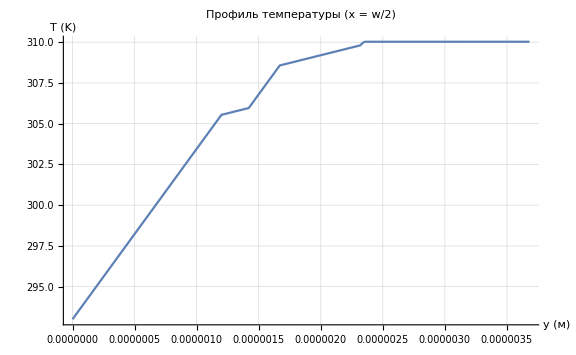

```mathematica
(* ==========ВСПОМОГАТЕЛЬНЫЙ КОД==========*)(*Функция температуры в слое i в точке y (частное решение)*)TlayerPart[i_,y_]:=q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0)

(*Массивы для удобства*)
q={q1,q2,q3,q4,q5,q6,q7,q8,q9};
k={k1,k2,k3,k4,k5,k6,k7,k8,k9};
yBoundary={0,y1,y2,y3,y4,y5,y6,y7,y8,y9};

(*Функция для вычисления вклада всех однородных мод*)
ThPoint[x_,y_]:=Module[{sum=0},Do[n=s[[1]];
α=(π n)/w;
sol=s[[2]];
sum+=((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x];,{s,solsN}];
sum]

(*Вычисляем температуру на каждой границе (частное решение)*)
tempsPart=Table[Which[y==0,TlayerPart[1,0],y==y1,TlayerPart[1,y1],y==y2,TlayerPart[2,y2],y==y3,TlayerPart[3,y3],y==y4,TlayerPart[4,y4],y==y5,TlayerPart[5,y5],y==y6,TlayerPart[6,y6],y==y7,TlayerPart[7,y7],y==y8,TlayerPart[8,y8],y==y9,TlayerPart[9,y9]],{y,yBoundary}];

(*Если есть однородные моды—добавляем их вклад*)
If[ValueQ[solsN]&&solsN=!={},tempsTotal=tempsPart+(ThPoint[w/2,#]&/@yBoundary);,tempsTotal=tempsPart;];

(*Вывод в консоль*)
Print["Температура на границах слоёв (x = w/2):"];
Print["y = 0      : T = ",tempsTotal[[1]]," K"];
Print["y = y1     : T = ",tempsTotal[[2]]," K"];
Print["y = y2     : T = ",tempsTotal[[3]]," K"];
Print["y = y3     : T = ",tempsTotal[[4]]," K"];
Print["y = y4     : T = ",tempsTotal[[5]]," K"];
Print["y = y5     : T = ",tempsTotal[[6]]," K"];
Print["y = y6     : T = ",tempsTotal[[7]]," K"];
Print["y = y7     : T = ",tempsTotal[[8]]," K"];
Print["y = y8     : T = ",tempsTotal[[9]]," K"];
Print["y = y9     : T = ",tempsTotal[[10]]," K"];

(*Построение графика*)
(* ==========ГЛАДКИЙ ПРОФИЛЬ ТЕМПЕРАТУРЫ==========*)(*Непрерывная функция температуры по y (при x=w/2)*)Tcontinuous[y_]:=Module[{i,Tp,Th},(*Определяем слой*)Which[0≤y≤y1,i=1,y1<y≤y2,i=2,y2<y≤y3,i=3,y3<y≤y4,i=4,y4<y≤y5,i=5,y5<y≤y6,i=6,y6<y≤y7,i=7,y7<y≤y8,i=8,y8<y≤y9,i=9,True,i=0];
If[i==0,Return[Null]];
(*Частное решение*)Tp=q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0);
(*Однородные моды*)Th=If[ValueQ[solsN]&&solsN=!={},Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α (w/2)]],{s,solsN}],0];
Tp+Th];

(*Строим гладкий график*)
Plot[Tcontinuous[y],{y,0,y9},AxesLabel->{"y (м)","T (K)"},PlotLabel->"Профиль температуры (x = w/2)",GridLines->Automatic,ImageSize->Large,PlotRange->All]
```

```mathematica
In[1436]:=
```

```mathematica
(* ==========ГЛАДКИЙ ПРОФИЛЬ ТЕМПЕРАТУРЫ==========*)(*Непрерывная функция температуры по y (при x=w/2)*)Tcontinuous[y_]:=Module[{i,Tp,Th},Which[0≤y≤y1,i=1,y1<y≤y2,i=2,y2<y≤y3,i=3,y3<y≤y4,i=4,y4<y≤y5,i=5,y5<y≤y6,i=6,y6<y≤y7,i=7,y7<y≤y8,i=8,y8<y≤y9,i=9,True,i=0];
If[i==0,Return[Null]];
(*Частное решение*)Tp=q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0);
(*Однородные моды*)Th=If[ValueQ[solsN]&&solsN=!={},Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α (w/2)]],{s,solsN}],0];
Tp+Th];

(*Построение гладкого графика с осью y в микрометрах*)
Plot[Tcontinuous[y],{y,0,y9},AxesLabel->{"y (мкм)","T (K)"},PlotLabel->Style["Профиль температуры (x = w/2)",Bold,14],GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotStyle->{Thick,Blue},LabelStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameLabel->{"y (мкм)","T (K)"},FrameStyle->Directive[Black,12],Axes->False,Background->White]/.{y_Real:>y*10^6}
```

```mathematica
Out[1437]=
```

y = y9     : T = 293.071 K

y = y8     : T = 293.071 K

y = y7     : T = 293.071 K

y = y6     : T = 293.071 K

y = y5     : T = 293.071 K

y = y4     : T = 293.071 K

y = y3     : T = 293.061 K

y = y2     : T = 293.039 K

y = y1     : T = 293.019 K

y = 0      : T = 293. K

"

y = 0      : T = 293. K

y = y1     : T = 293.116 K

y = y2     : T = 293.233 K

y = y3     : T = 293.365 K

y = y4     : T = 293.426 K

y = y5     : T = 293.428 K

y = y6     : T = 293.429 K

y = y7     : T = 293.429 K

y = y8     : T = 293.429 K

y = y9     : T = 293.429 K

y = y9     : T = 293.429 K

```mathematica
In[]:=
```

```mathematica
(* ===ВЫЧИСЛЕНИЕ ТЕМПЕРАТУРЫ НА ГРАНИЦАХ СЛОЁВ===*)(*Задаём x,для которого считаем*)x0=w/2;(*можно заменить на 0,w/2,w*)Print["x = ",x0*10^6," мкм"];

(*Частное решение на границах слоёв*)
Print["\nЧАСТНОЕ РЕШЕНИЕ (n=0):"];
Print["y = 0      : T = ",(B0[1]/.sol0)];
Print["y = y1     : T = ",(q1/(2 k1) y1^2+(A0[1]/.sol0) y1+(B0[1]/.sol0))];
Print["y = y2     : T = ",(q2/(2 k2) y2^2+(A0[2]/.sol0) y2+(B0[2]/.sol0))];
Print["y = y3     : T = ",(q3/(2 k3) y3^2+(A0[3]/.sol0) y3+(B0[3]/.sol0))];
Print["y = y4     : T = ",(q4/(2 k4) y4^2+(A0[4]/.sol0) y4+(B0[4]/.sol0))];
Print["y = y5     : T = ",(q5/(2 k5) y5^2+(A0[5]/.sol0) y5+(B0[5]/.sol0))];
Print["y = y6     : T = ",(q6/(2 k6) y6^2+(A0[6]/.sol0) y6+(B0[6]/.sol0))];
Print["y = y7     : T = ",(q7/(2 k7) y7^2+(A0[7]/.sol0) y7+(B0[7]/.sol0))];
Print["y = y8     : T = ",(q8/(2 k8) y8^2+(A0[8]/.sol0) y8+(B0[8]/.sol0))];
Print["y = y9     : T = ",(q9/(2 k9) y9^2+(A0[9]/.sol0) y9+(B0[9]/.sol0))];

(*Если есть однородные моды—выводим их вклад*)
If[ValueQ[solsN]&&solsN=!={},Print["\nВКЛАД ОДНОРОДНЫХ МОД ПРИ x = ",x0*10^6," мкм:"];
(*Функция для вычисления вклада всех мод в точке (x,y)*)ThPoint[x_,y_]:=Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x]],{s,solsN}];
Print["y = 0      : Th = ",ThPoint[x0,0]];
Print["y = y1     : Th = ",ThPoint[x0,y1]];
Print["y = y2     : Th = ",ThPoint[x0,y2]];
Print["y = y3     : Th = ",ThPoint[x0,y3]];
Print["y = y4     : Th = ",ThPoint[x0,y4]];
Print["y = y5     : Th = ",ThPoint[x0,y5]];
Print["y = y6     : Th = ",ThPoint[x0,y6]];
Print["y = y7     : Th = ",ThPoint[x0,y7]];
Print["y = y8     : Th = ",ThPoint[x0,y8]];
Print["y = y9     : Th = ",ThPoint[x0,y9]];
Print["\nПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = ",x0*10^6," мкм:"];
Print["y = 0      : T = ",(B0[1]/.sol0)+ThPoint[x0,0]];
Print["y = y1     : T = ",(q1/(2 k1) y1^2+(A0[1]/.sol0) y1+(B0[1]/.sol0))+ThPoint[x0,y1]];
Print["y = y2     : T = ",(q2/(2 k2) y2^2+(A0[2]/.sol0) y2+(B0[2]/.sol0))+ThPoint[x0,y2]];
Print["y = y3     : T = ",(q3/(2 k3) y3^2+(A0[3]/.sol0) y3+(B0[3]/.sol0))+ThPoint[x0,y3]];
Print["y = y4     : T = ",(q4/(2 k4) y4^2+(A0[4]/.sol0) y4+(B0[4]/.sol0))+ThPoint[x0,y4]];
Print["y = y5     : T = ",(q5/(2 k5) y5^2+(A0[5]/.sol0) y5+(B0[5]/.sol0))+ThPoint[x0,y5]];
Print["y = y6     : T = ",(q6/(2 k6) y6^2+(A0[6]/.sol0) y6+(B0[6]/.sol0))+ThPoint[x0,y6]];
Print["y = y7     : T = ",(q7/(2 k7) y7^2+(A0[7]/.sol0) y7+(B0[7]/.sol0))+ThPoint[x0,y7]];
Print["y = y8     : T = ",(q8/(2 k8) y8^2+(A0[8]/.sol0) y8+(B0[8]/.sol0))+ThPoint[x0,y8]];
Print["y = y9     : T = ",(q9/(2 k9) y9^2+(A0[9]/.sol0) y9+(B0[9]/.sol0))+ThPoint[x0,y9]];,Print["\n(Однородные моды не найдены или не заданы.)"]].
```

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0      : T = 293.

y = y1     : T = 293.056

y = y2     : T = 293.112

y = y3     : T = 293.175

y = y4     : T = 293.204

y = y5     : T = 293.204

y = y6     : T = 293.172

y = y7     : T = 293.131

y = y8     : T = 293.035

y = y9     : T = 293.026

```mathematica
(* ==========ПОСТРОЕНИЕ ТЕПЛОВОЙ КАРТЫ==========*)(*Задаём координатную сетку*)nx=200;(*число точек по x*)ny=500;(*число точек по y*)xGrid=Subdivide[0,w,nx];
yGrid=Subdivide[0,y9,ny];

(*Функция температуры (частное+однородное)*)
Ttotal[x_,y_]:=Module[{Tp,Th},(*Частное решение (n=0)—слоистая структура*)Tp=Which[0≤y≤y1,q1/(2 k1) y^2+(A0[1]/.sol0) y+(B0[1]/.sol0),y1<y≤y2,q2/(2 k2) y^2+(A0[2]/.sol0) y+(B0[2]/.sol0),y2<y≤y3,q3/(2 k3) y^2+(A0[3]/.sol0) y+(B0[3]/.sol0),y3<y≤y4,q4/(2 k4) y^2+(A0[4]/.sol0) y+(B0[4]/.sol0),y4<y≤y5,q5/(2 k5) y^2+(A0[5]/.sol0) y+(B0[5]/.sol0),y5<y≤y6,q6/(2 k6) y^2+(A0[6]/.sol0) y+(B0[6]/.sol0),y6<y≤y7,q7/(2 k7) y^2+(A0[7]/.sol0) y+(B0[7]/.sol0),y7<y≤y8,q8/(2 k8) y^2+(A0[8]/.sol0) y+(B0[8]/.sol0),y8<y≤y9,q9/(2 k9) y^2+(A0[9]/.sol0) y+(B0[9]/.sol0)];
(*Однородные моды (n≥1)*)Th=If[ValueQ[solsN]&&solsN=!={},Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x]],{s,solsN}],0];
Tp+Th];

(*Вычисляем температуру на сетке*)
temperatureData=Table[Ttotal[x,y],{y,yGrid},{x,xGrid}];

(*Строим тепловую карту*)
ListDensityPlot[temperatureData,DataRange->{{0,w*10^6},{0,y9*10^9}},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"x (мкм)","y (нм)"},PlotLabel->"Распределение температуры T(x, y)",AspectRatio->0.5,ImageSize->Large]
```

```mathematica
(* ==========ГРАФИК T(y) В ЦЕНТРЕ СТРУКТУРЫ==========*)(*Функция полной температуры в зависимости от y (при x=w/2)*)Tprofile[y_]:=Module[{Tp,Th},(*Частное решение (n=0)*)Tp=Which[0≤y≤y1,q1/(2 k1) y^2+(A0[1]/.sol0) y+(B0[1]/.sol0),y1<y≤y2,q2/(2 k2) y^2+(A0[2]/.sol0) y+(B0[2]/.sol0),y2<y≤y3,q3/(2 k3) y^2+(A0[3]/.sol0) y+(B0[3]/.sol0),y3<y≤y4,q4/(2 k4) y^2+(A0[4]/.sol0) y+(B0[4]/.sol0),y4<y≤y5,q5/(2 k5) y^2+(A0[5]/.sol0) y+(B0[5]/.sol0),y5<y≤y6,q6/(2 k6) y^2+(A0[6]/.sol0) y+(B0[6]/.sol0),y6<y≤y7,q7/(2 k7) y^2+(A0[7]/.sol0) y+(B0[7]/.sol0),y7<y≤y8,q8/(2 k8) y^2+(A0[8]/.sol0) y+(B0[8]/.sol0),y8<y≤y9,q9/(2 k9) y^2+(A0[9]/.sol0) y+(B0[9]/.sol0)];
(*Вклад однородных мод (если есть)*)Th=If[ValueQ[solsN]&&solsN=!={},Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α w/2]],{s,solsN}],0];
Tp+Th];

(*Построение графика*)
Plot[Tprofile[y*10^9],{y,0,y9*10^9},AxesLabel->{"y (нм)","T (K)"},PlotLabel->"Температура по центру структуры (x = w/2)",GridLines->Automatic,PlotRange->All,ImageSize->Large]
```

-Graphics-

```mathematica
(*Очистка окружения*)ClearAll["Global`*"]

(*Параметры задачи (безразмерные)*)
hbar=1;m=1;a=1;U0=10;
(*Потенциал V(x)=U0*(1-x/a) для 0<x<a,и 0 вне*)

(*Функция для решения ОДУ внутри барьера*)
solveInside[alpha_,k_]:=Module[{sol,psi_a,psi_prime_a,F},(*Решаем ОДУ внутри барьера*)sol=NDSolveValue[{psi''[x]+(k^2-2*(1-x)) psi[x]==0,psi[0]==alpha,psi'[0]==I*k*(2-alpha)},{psi,psi'},{x,0,1},MaxSteps->10000,AccuracyGoal->10,PrecisionGoal->10];
psi_a=sol[[1]][1];
psi_prime_a=sol[[2]][1];
(*Условие уходящей волны:ψ'(a)/ψ(a)=i k*)F=psi_prime_a/psi_a-I*k;
Return[Abs[F]^2]]

(*Поиск alpha для заданного k*)
findAlpha[k_]:=Module[{result},result=FindMinimum[solveInside[{alphaRe,alphaIm}/.{alphaRe->Re[alpha],alphaIm->Im[alpha]},k],{{alphaRe,1},{alphaIm,0}},Method->"Newton"];
Return[result[[2]]/.{alphaRe->alpha,alphaIm->alpha}]]

(*Основной цикл по k*)
kMin=0.1;kMax=5.0;nK=300;
kVec=Subdivide[kMin,kMax,nK-1];
tVec=Table[0,{nK}];

Monitor[Do[k=kVec[[idx]];
(*Начальное приближение*)alpha0=1+0*I;
(*Минимизация невязки*)alphaOpt=findAlpha[k];
(*Решение внутри барьера с найденным alpha*)sol=NDSolveValue[{psi''[x]+(k^2-2*(1-x)) psi[x]==0,psi[0]==alphaOpt,psi'[0]==I*k*(2-alphaOpt)},psi,{x,0,1}];
psiA=sol[1];
(*Амплитуда прошедшей волны и коэффициент прохождения*)C=psiA*Exp[I*k*1];
T=Abs[C]^2;
tVec[[idx]]=T;,{idx,1,nK}],ProgressIndicator[idx,{1,nK}]]

(*График коэффициента прохождения*)
ListPlot[Transpose[{kVec,tVec}],Joined->True,PlotStyle->{Blue,Thickness[0.005]},AxesLabel->{"Волновой вектор k","Коэффициент прохождения T"},PlotLabel->"Прохождение через треугольный барьер",GridLines->Automatic,PlotRange->{{kMin,kMax},{0,1}},ImageSize->Large]

(*Построение квадрата волновой функции для выбранного k*)
kExample=2;

(*Находим alpha для kExample*)
alphaExample=findAlpha[kExample];
betaExample=I*kExample*(2-alphaExample);

(*Решение внутри барьера*)
solExample=NDSolveValue[{psi''[x]+(kExample^2-2*(1-x)) psi[x]==0,psi[0]==alphaExample,psi'[0]==betaExample},psi,{x,0,1}];

psiAExample=solExample[1];

(*Амплитуды*)
B=alphaExample-1;
C=psiAExample*Exp[-I*kExample*1];

(*Область x<0*)
xLeft=Subdivide[-2,0,200];
psiLeft=Exp[I*kExample*xLeft]+B*Exp[-I*kExample*xLeft];
psiLeftAbs2=Abs[psiLeft]^2;

(*Область x>a*)
xRight=Subdivide[1,3,200];
psiRight=C*Exp[I*kExample*xRight];
psiRightAbs2=Abs[psiRight]^2;

(*Область внутри барьера*)
xInside=Subdivide[0,1,200];
psiInside=solExample[xInside];
psiInsideAbs2=Abs[psiInside]^2;

(*Сшиваем*)
xFull=Join[xLeft,xInside,xRight];
psi2Full=Join[psiLeftAbs2,psiInsideAbs2,psiRightAbs2];

(*Потенциал для визуализации*)
xPot=Subdivide[-0.2,1.2,200];
vPot=U0*(1-Min[1,Max[0,#/a]])&/@xPot;
vPotScaled=vPot/Max[vPot];

(*График квадрата волновой функции*)
ListLinePlot[{Transpose[{xFull,psi2Full}],Transpose[{xPot,vPotScaled}]},PlotStyle->{{Red,Thickness[0.01]},{Black,Dashed,Thickness[0.005]}},AxesLabel->{"x","|ψ(x)|.b2"},PlotLabel->StringForm["Квадрат волновой функции при k = ``",kExample],GridLines->Automatic,PlotLegends->{"|ψ(x)|.b2","Потенциал (вид)"},ImageSize->Large]
```

Module::lvsym: Local variable specification {sol$,psi_a,psi_prime _a,F$} contains psi_a, which is not a symbol or an assignment to a symbol.

General::stop: Further output of Module::lvsym will be suppressed during this calculation.

FindMinimum::nrnum: The function value Module[{sol$,psi_a,psi_prime _a,F$},sol$=(Compile`$16=Re[alpha];Compile`$17=Im[alpha];NDSolveValue[{Plus[«2»]==0,psi[«1»]=={«2»},(«1»)^(«1»)[«1»]==Times[«3»]},{psi,psi'},{x,0,1},MaxSteps→10000,AccuracyGoal→10,PrecisionGoal→10]);psi$_a=sol$⟦1⟧[1];«1»;F$=«1»;Return[Abs[F$]^2]] is not a real number at {alphaRe,alphaIm} = {1.,0.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

NDSolveValue::ndinnt: Initial condition {{alpha,1.},{alpha,0.}} is not a number or a rectangular array of numbers.

Set::wrsym: Symbol C is Protected.

NDSolveValue::ndinnt: Initial condition {{alpha,1.},{alpha,0.}} is not a number or a rectangular array of numbers.

Set::wrsym: Symbol C is Protected.

NDSolveValue::ndinnt: Initial condition {{alpha,1.},{alpha,0.}} is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolveValue::ndinnt will be suppressed during this calculation.

Set::wrsym: Symbol C is Protected.

General::stop: Further output of Set::wrsym will be suppressed during this calculation.

-Graphics-

Module::lvsym: Local variable specification {sol$,psi_a,psi_prime _a,F$} contains psi_a, which is not a symbol or an assignment to a symbol.

General::stop: Further output of Module::lvsym will be suppressed during this calculation.

FindMinimum::nrnum: The function value Module[{sol$,psi_a,psi_prime _a,F$},sol$=(Compile`$16=Re[alpha];Compile`$17=Im[alpha];NDSolveValue[{Plus[«2»]==0,psi[«1»]=={«2»},(«1»)^(«1»)[«1»]==Times[«3»]},{psi,psi'},{x,0,1},MaxSteps→10000,AccuracyGoal→10,PrecisionGoal→10]);psi$_a=sol$⟦1⟧[1];«1»;F$=«1»;Return[Abs[F$]^2]] is not a real number at {alphaRe,alphaIm} = {1.,0.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

NDSolveValue::ndinnt: Initial condition {{alpha,1.},{alpha,0.}} is not a number or a rectangular array of numbers.

Set::wrsym: Symbol C is Protected.

Thread::tdlen: Objects of unequal length in {{-1+alpha,0},{-1+alpha,-1}} {ⅇ^(4 ⅈ),ⅇ^((199 ⅈ)/50),ⅇ^((99 ⅈ)/25),ⅇ^((197 ⅈ)/50),ⅇ^((98 ⅈ)/25),ⅇ^((39 ⅈ)/10),ⅇ^((97 ⅈ)/25),ⅇ^((193 ⅈ)/50),ⅇ^((96 ⅈ)/25),ⅇ^((191 ⅈ)/50),ⅇ^((19 ⅈ)/5),ⅇ^((189 ⅈ)/50),ⅇ^((94 ⅈ)/25),«26»,ⅇ^((161 ⅈ)/50),ⅇ^((16 ⅈ)/5),ⅇ^((159 ⅈ)/50),ⅇ^((79 ⅈ)/25),ⅇ^((157 ⅈ)/50),ⅇ^((78 ⅈ)/25),ⅇ^((31 ⅈ)/10),ⅇ^((77 ⅈ)/25),ⅇ^((153 ⅈ)/50),ⅇ^((76 ⅈ)/25),ⅇ^((151 ⅈ)/50),«151»} cannot be combined.

Join::heads: Heads List and Power at positions 1 and 2 are expected to be the same.

Transpose::nmtx: The first two levels of {{-2,-199/100,-99/50,-197/100,-49/25,-39/20,-97/50,-193/100,-48/25,-191/100,-19/10,-189/100,-47/25,-187/100,-93/50,-37/20,-46/25,-183/100,-91/50,«13»,-42/25,-167/100,-83/50,-33/20,-41/25,-163/100,-81/50,-161/100,-8/5,-159/100,-79/50,-157/100,-39/25,-31/20,-77/50,-153/100,-38/25,-151/100,«553»},«1»} cannot be transposed.

Thread::tdlen: Objects of unequal length in {{-1.+alpha,0},{-1.+alpha,-1.}} {-0.653643620863612-0.7568024953079283 ⅈ,«49»,«151»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

NDSolveValue::ndinnt: Initial condition {{alpha,1.},{alpha,0.}} is not a number or a rectangular array of numbers.

Join::heads: Heads List and Power at positions 1 and 2 are expected to be the same.

Transpose::nmtx: The first two levels of {{-2.,-1.99,-1.98,-1.97,-1.96,-1.95,-1.94,-1.93,-1.92,-1.91,-1.9,-1.89,-1.88,«25»,-1.62,-1.61,-1.6,-1.59,-1.58,-1.57,-1.56,-1.55,-1.54,-1.53,-1.52,-1.51,«553»},«1»} cannot be transposed.

NDSolveValue::ndinnt: Initial condition {{alpha,1.},{alpha,0.}} is not a number or a rectangular array of numbers.

Join::heads: Heads List and Power at positions 1 and 2 are expected to be the same.

Transpose::nmtx: The first two levels of {{-2.,-1.99,-1.98,-1.97,-1.96,-1.95,-1.94,-1.93,-1.92,-1.91,-1.9,-1.89,-1.88,-1.87,-1.86,-1.85,-1.84,-1.83,-1.82,«14»,-1.67,-1.66,-1.65,-1.64,-1.63,-1.62,-1.61,-1.6,-1.59,-1.58,-1.57,-1.56,-1.55,-1.54,-1.53,-1.52,-1.51,«553»},«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

NDSolveValue::ndinnt: Initial condition {{alpha,1.},{alpha,0.}} is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolveValue::ndinnt will be suppressed during this calculation.

Join::heads: Heads List and Power at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

ListLinePlot::lpn: {{},{{-0.2,1.},{-0.193,1.},{-0.186,1.},{-0.179,1.},{-0.172,1.},«41»,{0.122,0.878},{0.129,0.871},{0.136,0.864},{0.143,0.857},«151»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[1]
 |  |  |  |

Set::wrsym: Symbol ⅇ is Protected.

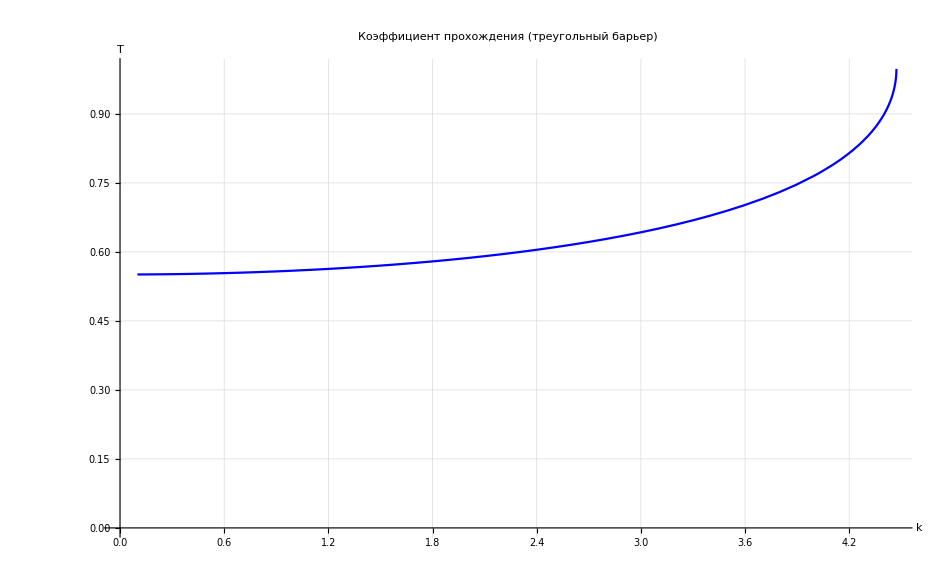

```mathematica
ClearAll["Global`*"]

(*Параметры*)
a=1;U0=10;

(*Прямое вычисление коэффициента прохождения*)
transmission[k_]:=Module[{alpha,beta,Ai,Bi,psiA,psiPrimeA,C,T},(*Используем функции Эйри для треугольного барьера*)(*Переменная:z=(2m/(hbar^2))^(1/3)*(U0*(1-x/a)-E)*)(*В безразмерных единицах:*)E=k^2/2;
Vmax=U0;
(*Точки поворота*)x1=0;
x2=a*(1-E/Vmax);
If[x2≤0||x2≥a,Return[1.0];(*Надбарьерное прохождение*)];
(*Аппроксимация WKB для коэффициента прохождения*)(*Формула для треугольного барьера:T≈exp(-4/3*sqrt(2m/hbar^2)*(U0-E)^(3/2)*a/U0)*)T=Exp[-(4/3)*Sqrt[2*U0-k^2]*a/U0];
Return[T]]

(*Построение графика*)
kMin=0.1;kMax=5.0;
Plot[transmission[k],{k,kMin,kMax},PlotStyle->Blue,AxesLabel->{"k","T"},PlotLabel->"Коэффициент прохождения (треугольный барьер)",GridLines->Automatic,PlotRange->{0,1}]
```

```mathematica
(* ==========РАСЧЁТ q_i ДЛЯ ВСЕХ ТОКОВ==========*)L=4*10^-3;
w=400*10^-6;
S=L*w;
S2=S^2;
dact=42*10^-9;
Vact=L*w*dact;

ρ={6.25*10^-4,1.3*10^-4,2.5*10^-3,7.8*10^-3,0,4.17*10^-3,1.39*10^-3,3.9*10^-4,2.23*10^-5};

(*Экспериментальные точки*)
Iexp={1.0,2.0,3.0,4.0,5.0,6.0,7.0,8.0,9.0,10.0};
Uexp={1.205,1.244,1.279,1.311,1.341,1.370,1.398,1.426,1.450,1.480};
Pexp={0.32,1.102,1.874,2.641,3.384,4.089,4.840,5.504,6.221,6.876};

(*Функции интерполяции*)
U=Interpolation[Transpose[{Iexp,Uexp}],InterpolationOrder->1];
Pout=Interpolation[Transpose[{Iexp,Pexp}],InterpolationOrder->1];

(*Генерация строк для всех токов*)
Do[Icurr=i;
Print["Ток I = ",Icurr," A"];
(*Для слоёв 1-4,6-9*)Do[If[j==5,Continue[]];
qj=(Icurr^2*ρ[[j]])/S2;
Print["q",j," = ",qj];,{j,1,9}];
(*Активная область*)qact=(U[Icurr]*Icurr-Pout[Icurr])/Vact;
Print["q5 = ",qact];
Print["-----------------------"];,{i,Iexp}];
```

Ток I = 1. A

q1 = 2.44141×10^8

q2 = 5.07813×10^7

q3 = 9.76563×10^8

q4 = 3.04688×10^9

q6 = 1.62891×10^9

q7 = 5.42969×10^8

q8 = 1.52344×10^8

q9 = 8.71094×10^6

q5 = 1.31696×10^13

-----------------------

Ток I = 2. A

q1 = 9.76563×10^8

q2 = 2.03125×10^8

q3 = 3.90625×10^9

q4 = 1.21875×10^10

q6 = 6.51563×10^9

q7 = 2.17188×10^9

q8 = 6.09375×10^8

q9 = 3.48438×10^7

q5 = 2.0625×10^13

-----------------------

Ток I = 3. A

q1 = 2.19727×10^9

q2 = 4.57031×10^8

q3 = 8.78906×10^9

q4 = 2.74219×10^10

q6 = 1.46602×10^10

q7 = 4.88672×10^9

q8 = 1.37109×10^9

q9 = 7.83984×10^7

q5 = 2.92113×10^13

-----------------------

Ток I = 4. A

q1 = 3.90625×10^9

q2 = 8.125×10^8

q3 = 1.5625×10^10

q4 = 4.875×10^10

q6 = 2.60625×10^10

q7 = 8.6875×10^9

q8 = 2.4375×10^9

q9 = 1.39375×10^8

q5 = 3.87351×10^13

-----------------------

Ток I = 5. A

q1 = 6.10352×10^9

q2 = 1.26953×10^9

q3 = 2.44141×10^10

q4 = 7.61719×10^10

q6 = 4.07227×10^10

q7 = 1.35742×10^10

q8 = 3.80859×10^9

q9 = 2.17773×10^8

q5 = 4.94196×10^13

-----------------------

Ток I = 6. A

q1 = 8.78906×10^9

q2 = 1.82813×10^9

q3 = 3.51563×10^10

q4 = 1.09688×10^11

q6 = 5.86406×10^10

q7 = 1.95469×10^10

q8 = 5.48438×10^9

q9 = 3.13594×10^8

q5 = 6.14732×10^13

-----------------------

Ток I = 7. A

q1 = 1.19629×10^10

q2 = 2.48828×10^9

q3 = 4.78516×10^10

q4 = 1.49297×10^11

q6 = 7.98164×10^10

q7 = 2.66055×10^10

q8 = 7.46484×10^9

q9 = 4.26836×10^8

q5 = 7.36012×10^13

-----------------------

Ток I = 8. A

q1 = 1.5625×10^10

q2 = 3.25×10^9

q3 = 6.25×10^10

q4 = 1.95×10^11

q6 = 1.0425×10^11

q7 = 3.475×10^10

q8 = 9.75×10^9

q9 = 5.575×10^8

q5 = 8.78571×10^13

-----------------------

Ток I = 9. A

q1 = 1.97754×10^10

q2 = 4.11328×10^9

q3 = 7.91016×10^10

q4 = 2.46797×10^11

q6 = 1.31941×10^11

q7 = 4.39805×10^10

q8 = 1.23398×10^10

q9 = 7.05586×10^8

q5 = 1.01622×10^14

-----------------------

Ток I = 10. A

q1 = 2.44141×10^10

q2 = 5.07813×10^9

q3 = 9.76563×10^10

q4 = 3.04687×10^11

q6 = 1.62891×10^11

q7 = 5.42969×10^10

q8 = 1.52344×10^10

q9 = 8.71094×10^8

q5 = 1.17917×10^14

-----------------------

```mathematica
(* ==========ГЛАДКИЙ ПРОФИЛЬ ТЕМПЕРАТУРЫ==========*)(*Непрерывная функция температуры по y (при x=w/2)*)Tcontinuous[y_]:=Module[{i,Tp,Th},Which[0≤y≤y1,i=1,y1<y≤y2,i=2,y2<y≤y3,i=3,y3<y≤y4,i=4,y4<y≤y5,i=5,y5<y≤y6,i=6,y6<y≤y7,i=7,y7<y≤y8,i=8,y8<y≤y9,i=9,True,i=0];
If[i==0,Return[Null]];
(*Частное решение*)Tp=q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0);
(*Однородные моды*)Th=If[ValueQ[solsN]&&solsN=!={},Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α (w/2)]],{s,solsN}],0];
Tp+Th];

(*Построение гладкого графика с осью y в микрометрах*)
Plot[Tcontinuous[y],{y,0,y9},AxesLabel->{"y (мкм)","T (K)"},PlotLabel->Style["Профиль температуры (x = w/2)",Bold,14],GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotStyle->{Thick,Blue},LabelStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameLabel->{"y (мкм)","T (K)"},FrameStyle->Directive[Black,12],Axes->False,Background->White]/.{y_Real:>y*10^6}
```

```mathematica
(* ==========ТЕПЛОВАЯ КАРТА==========*)(*Непрерывная функция полной температуры*)Tfull[x_,y_]:=Module[{i,Tp,Th},Which[0≤y≤y1,i=1,y1<y≤y2,i=2,y2<y≤y3,i=3,y3<y≤y4,i=4,y4<y≤y5,i=5,y5<y≤y6,i=6,y6<y≤y7,i=7,y7<y≤y8,i=8,y8<y≤y9,i=9,True,i=0];
If[i==0,Return[Null]];
Tp=q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0);
Th=If[ValueQ[solsN]&&solsN=!={},Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x]],{s,solsN}],0];
Tp+Th];

(*Создаём сетку*)
nx=300;
ny=500;
xGrid=Subdivide[0,w,nx];
yGrid=Subdivide[0,y9,ny];

(*Вычисляем температуру на сетке*)
temperatureData=Table[Tfull[x,y],{y,yGrid},{x,xGrid}];

(*Строим тепловую карту*)
ListDensityPlot[temperatureData,DataRange->{{0,w*10^6},{0,y9*10^6}},ColorFunction->"TemperatureMap",PlotLegends->BarLegend[Automatic,LegendLabel->"T (K)"],FrameLabel->{"x (мкм)","y (мкм)"},PlotLabel->Style["Распределение температуры T(x, y)",Bold,14],ImageSize->Large,AspectRatio->0.5,FrameStyle->Directive[Black,12],LabelStyle->{FontFamily->"Times",FontSize->12},PlotRange->All,InterpolationOrder->1]
```

-Graphics-

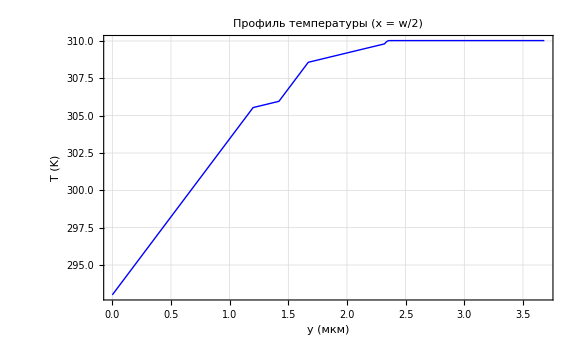

```mathematica
(* ==========ГЛАДКИЙ ПРОФИЛЬ ТЕМПЕРАТУРЫ==========*)(*Непрерывная функция температуры по y (при x=w/2),y в метрах*)Tcontinuous[y_]:=Module[{i,Tp,Th},Which[0≤y≤y1,i=1,y1<y≤y2,i=2,y2<y≤y3,i=3,y3<y≤y4,i=4,y4<y≤y5,i=5,y5<y≤y6,i=6,y6<y≤y7,i=7,y7<y≤y8,i=8,y8<y≤y9,i=9,True,i=0];
If[i==0,Return[Null]];
Tp=q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0);
Th=If[ValueQ[solsN]&&solsN=!={},Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α (w/2)]],{s,solsN}],0];
Tp+Th];

(*Строим график:преобразуем y из микрометров в метры на лету*)
Plot[Tcontinuous[y*10^-6],{y,0,y9*10^6},AxesLabel->{"y (мкм)","T (K)"},PlotLabel->Style["Профиль температуры (x = w/2)",Bold,14],GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotStyle->{Thick,Blue},LabelStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameLabel->{"y (мкм)","T (K)"},FrameStyle->Directive[Black,12],Axes->False,Background->White]
```